正在生成高相干宇宙背景 (Window=200)...

当前活性表皮节点数: 6862

正在定位拓扑双缝源...

正在渲染【全息骨架】上的宏观干涉条纹...

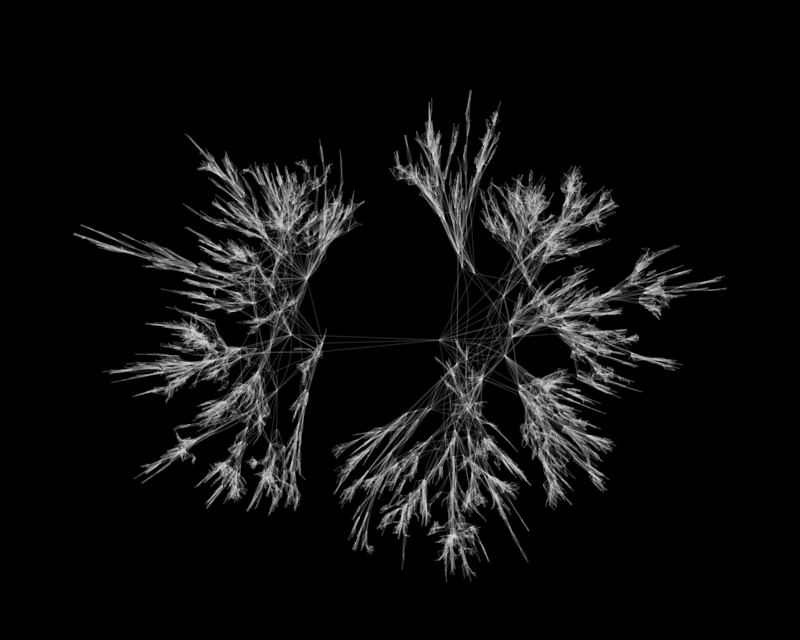

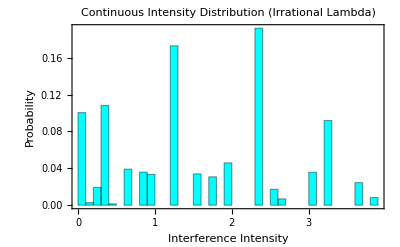

```mathematica
ClearAll["Global`*"];
SeedRandom[1234]; 

(* 1. 超高速大视界并发引擎 (Window = 200) *)
StepEvolution[g_Graph, window_] := Module[
  {allEdges, activeEdges, nActive, used, updates,
   tempE1, tempE2, e1List, x, y, z, wCounter, newVertices,
   newActive, newFrozen, remainingEdges},
  
  allEdges = EdgeList[g];
  activeEdges = RandomSample[Cases[allEdges, _UndirectedEdge]];
  nActive = Length[activeEdges];
  If[nActive < 2, Return[g]];
  
  used = ConstantArray[False, nActive]; 
  updates = {};
  
  Do[
    If[!used[[i]],
      tempE1 = activeEdges[[i]];
      e1List = List @@ tempE1;
      Do[
        If[!used[[j]],
          tempE2 = activeEdges[[j]];
          If[Length[Intersection[e1List, List @@ tempE2]] == 1,
            AppendTo[updates, {tempE1, tempE2}];
            used[[i]] = True;
            used[[j]] = True;
            Break[];
          ]
        ],
        {j, i + 1, Min[i + window, nActive]} 
      ]
    ],
    {i, 1, nActive}
  ];
  
  If[Length[updates] == 0, Return[g]];
  wCounter = Max[VertexList[g]];
  newVertices = {}; newActive = {}; newFrozen = {};
  
  Do[
    y = Intersection[List @@ pair[[1]], List @@ pair[[2]]][[1]];
    x = Complement[List @@ pair[[1]], {y}][[1]];
    z = Complement[List @@ pair[[2]], {y}][[1]];
    wCounter = wCounter + 1;
    AppendTo[newVertices, wCounter];
    newActive = Join[newActive, {UndirectedEdge[x, z], UndirectedEdge[x, wCounter], UndirectedEdge[wCounter, z]}];
    newFrozen = Join[newFrozen, {DirectedEdge[x, y], DirectedEdge[y, z]}];,
    {pair, updates}
  ];
  
  remainingEdges = Complement[allEdges, Flatten[updates]];
  Graph[VertexList[g] ~Join~ newVertices, Union[remainingEdges, newActive, newFrozen]]
];

(* 2. 初始化与背景演化 *)
vA = Range[1, 8]; eA = EdgeList[CompleteGraph[8]];
vB = Range[9, 14]; eB = EdgeList[CompleteGraph[6]] /. (i_Integer :> i + 8);
bridge = {UndirectedEdge[8, 9]};
initG = Graph[Join[vA, vB], Join[eA, eB, bridge]];

steps = 40; 
evolutionHistory = {initG};
Print[Style["正在生成高相干宇宙背景 (Window=200)...", Orange, Bold]];
Monitor[
  Do[AppendTo[evolutionHistory, StepEvolution[Last[evolutionHistory], 100]], {i, 1, steps}],
  Row[{"已演化步数: ", i, "/", steps}]
];

(* 3. 【核心修正】提取全息骨架与活性波前 *)
finalG = Last[evolutionHistory];

(* 提取表皮：只用来观测和寻找波源 *)
activeEdges = Cases[EdgeList[finalG], _UndirectedEdge];
activeG = Graph[activeEdges];
activeNodes = VertexList[activeG];
Print["当前活性表皮节点数: ", Length[activeNodes]];

(* 提取骨架：把全图（包含冻结边）转为无向流形，作为波传播的真实介质 *)
bulkG = Graph[VertexList[finalG], UndirectedEdge @@@ EdgeList[finalG]];

(* 4. 寻找“双缝”源 (S1 和 S2) *)
Print["正在定位拓扑双缝源..."];
s1 = RandomChoice[activeNodes];
(* 注意：现在的距离条件是基于全息骨架 bulkG 寻找的 *)
s2Candidates = Select[activeNodes, GraphDistance[bulkG, s1, #] == 6 &];
s2 = If[Length[s2Candidates] > 0, First[s2Candidates], RandomChoice[activeNodes]];

(* 5. 穿透骨架的干涉计算 *)
(* 信号通过宇宙的底层骨架进行传播测距，彻底避免表皮断裂带来的 Infinity *)
d1 = N[GraphDistance[bulkG, s1, #]] & /@ activeNodes;
d2 = N[GraphDistance[bulkG, s2, #]] & /@ activeNodes;

(* ===== 替换原来的第 6 步和第 7 步 ===== *)

(* 微调波长为无理数，打破相位的整数锁死，涌现连续光谱 *)
lambda = 20.0; 
intensity = (Cos[(2.0 * Pi * d1) / lambda] + Cos[(2.0 * Pi * d2) / lambda])^2;

Print[Style["正在渲染【全息骨架】上的宏观干涉条纹...", Blue, Bold]];
colors = Blend[{{0, Black}, {1, Darker[Blue]}, {2, Cyan}, {3, Yellow}, {4, White}}, #/4] & /@ intensity;

(* 核心：渲染完整的 bulkG，而不是破碎的表皮，提取最大连通图以防万一 *)
mainSpacetime = First[ConnectedGraphComponents[bulkG]];
plotNodes = VertexList[mainSpacetime];
plotColors = Thread[activeNodes -> colors]; 
(* 将非活性节点（历史骨架）染成暗灰色，作为背景衬托 *)
finalColors = # -> If[MemberQ[activeNodes, #], # /. plotColors, Darker[Gray, 0.8]] & /@ plotNodes;

plotInterference = GraphPlot[mainSpacetime,
  VertexStyle -> finalColors,
  VertexSize -> If[MemberQ[activeNodes, #], 0.8, 0.2] & /@ plotNodes,
  EdgeStyle -> Directive[Opacity[0.15], LightGray],
  PlotLabel -> Style["Macroscopic Double-Slit in Connected Spacetime", 14, Bold],
  Background -> Black,
  ImageSize -> 800
];

Print[plotInterference];

histogram = Histogram[intensity, 30, "Probability",
  Frame -> True, FrameLabel -> {"Interference Intensity", "Probability"},
  PlotLabel -> "Continuous Intensity Distribution (Irrational Lambda)",
  ChartStyle -> Cyan, ImageSize -> 400
];
Print[histogram];
```

1. 正在生成高相干宇宙背景 (纯净叠加态)...

正在定位拓扑双缝源...

2. 宏观探测器接入 S1，引发拓扑强退相干！

3. 渲染坍缩后的概率分布...

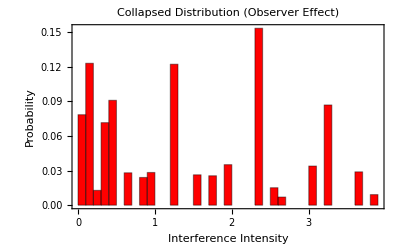

[终极判决]

对比上一张带有多个波峰的干涉图，观察这张红色的直方图：

```mathematica
ClearAll["Global`*"];
SeedRandom[1234]; 

(* 1. 超高速大视界并发引擎 (Window = 200) *)
StepEvolution[g_Graph, window_] := Module[
  {allEdges, activeEdges, nActive, used, updates,
   tempE1, tempE2, e1List, x, y, z, wCounter, newVertices,
   newActive, newFrozen, remainingEdges},
  
  allEdges = EdgeList[g];
  activeEdges = RandomSample[Cases[allEdges, _UndirectedEdge]];
  nActive = Length[activeEdges];
  If[nActive < 2, Return[g]];
  
  used = ConstantArray[False, nActive]; 
  updates = {};
  
  Do[
    If[!used[[i]],
      tempE1 = activeEdges[[i]];
      e1List = List @@ tempE1;
      Do[
        If[!used[[j]],
          tempE2 = activeEdges[[j]];
          If[Length[Intersection[e1List, List @@ tempE2]] == 1,
            AppendTo[updates, {tempE1, tempE2}];
            used[[i]] = True;
            used[[j]] = True;
            Break[];
          ]
        ],
        {j, i + 1, Min[i + window, nActive]} 
      ]
    ],
    {i, 1, nActive}
  ];
  
  If[Length[updates] == 0, Return[g]];
  wCounter = Max[VertexList[g]];
  newVertices = {}; newActive = {}; newFrozen = {};
  
  Do[
    y = Intersection[List @@ pair[[1]], List @@ pair[[2]]][[1]];
    x = Complement[List @@ pair[[1]], {y}][[1]];
    z = Complement[List @@ pair[[2]], {y}][[1]];
    wCounter = wCounter + 1;
    AppendTo[newVertices, wCounter];
    newActive = Join[newActive, {UndirectedEdge[x, z], UndirectedEdge[x, wCounter], UndirectedEdge[wCounter, z]}];
    newFrozen = Join[newFrozen, {DirectedEdge[x, y], DirectedEdge[y, z]}];,
    {pair, updates}
  ];
  
  remainingEdges = Complement[allEdges, Flatten[updates]];
  Graph[VertexList[g] ~Join~ newVertices, Union[remainingEdges, newActive, newFrozen]]
];

(* 2. 初始化与生成未观测的相干背景 (40步) *)
vA = Range[1, 8]; eA = EdgeList[CompleteGraph[8]];
vB = Range[9, 14]; eB = EdgeList[CompleteGraph[6]] /. (i_Integer :> i + 8);
bridge = {UndirectedEdge[8, 9]};
initG = Graph[Join[vA, vB], Join[eA, eB, bridge]];

steps = 40; 
evolutionHistory = {initG};
Print[Style["1. 正在生成高相干宇宙背景 (纯净叠加态)...", Orange, Bold]];
Monitor[
  Do[AppendTo[evolutionHistory, StepEvolution[Last[evolutionHistory], 100]], {i, 1, steps}],
  Row[{"已演化步数: ", i, "/", steps}]
];

finalG = Last[evolutionHistory];
activeNodes = VertexList[Graph[Cases[EdgeList[finalG], _UndirectedEdge]]];
bulkG = Graph[VertexList[finalG], UndirectedEdge @@@ EdgeList[finalG]];

(* 3. 寻找“双缝”源 S1 和 S2 *)
Print["正在定位拓扑双缝源..."];
s1 = RandomChoice[activeNodes];
s2Candidates = Select[activeNodes, GraphDistance[bulkG, s1, #] == 6 &];
s2 = If[Length[s2Candidates] > 0, First[s2Candidates], RandomChoice[activeNodes]];

(* 4. 引入宏观观测者（波函数坍缩开始！） *)
Print[Style["\n2. 宏观探测器接入 S1，引发拓扑强退相干！", Red, Bold]];

obsSize = 50; (* 这里可以随便改你的探测器“拓扑质量”，比如 50, 100, 150 *)

observerNodes = Range[Max[VertexList[finalG]] + 1, Max[VertexList[finalG]] + obsSize];
(* 制造一个极其致密的活性网络作为探测器 *)
observerEdges = EdgeList[CompleteGraph[obsSize]] /. (i_Integer :> observerNodes[[i]]);
(* 将探测器与 S1 进行拓扑纠缠（连接） *)
measurementEdge = {UndirectedEdge[s1, observerNodes[[1]]]};

measuredG = Graph[Join[VertexList[finalG], observerNodes], 
                  Join[EdgeList[finalG], observerEdges, measurementEdge]];

(* 让宇宙带着观测者再演化 10 步，确保算力被彻底抽干 *)
stepsDecoherence = 10; 
evolutionMeasured = {measuredG};
Monitor[
  Do[AppendTo[evolutionMeasured, StepEvolution[Last[evolutionMeasured], 100]], {i, 1, stepsDecoherence}],
  Row[{"测量互动进行中: ", i, "/", stepsDecoherence}]
];

(* 5. 提取坍缩后的全息骨架 *)
collapsedG = Last[evolutionMeasured];
bulkCollapsed = Graph[VertexList[collapsedG], UndirectedEdge @@@ EdgeList[collapsedG]];
activeNodesCollapsed = VertexList[Graph[Cases[EdgeList[collapsedG], _UndirectedEdge]]];

(* 6. 重新计算测地线相位 *)
d1 = N[GraphDistance[bulkCollapsed, s1, #]] & /@ activeNodesCollapsed;
d2 = N[GraphDistance[bulkCollapsed, s2, #]] & /@ activeNodesCollapsed;

lambda =20.0; 
intensityCollapsed = (Cos[(2.0 * Pi * d1) / lambda] + Cos[(2.0 * Pi * d2) / lambda])^2;

(* 7. 终极对比：坍缩后的直方图 *)
Print[Style["\n3. 渲染坍缩后的概率分布...", Red, Bold]];

histogramCollapsed = Histogram[intensityCollapsed, 30, "Probability",
  Frame -> True, FrameLabel -> {"Interference Intensity", "Probability"},
  PlotLabel -> Style["Collapsed Distribution (Observer Effect)", 14, Bold, Red],
  ChartStyle -> Red, ImageSize -> 400
];
Print[histogramCollapsed];

Print[Style["\n[终极判决]", Blue, Bold, 16]];
Print["对比上一张带有多个波峰的干涉图，观察这张红色的直方图："];
```